# CARBAPENEM RESISTANCE MODEL

## Data

### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

### Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="US_DDD"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}]; (*import data*)
data = data[[All,2;;]]; 
years = data[[1]];
tt = Length[years]; 
nop = (Length[data]-6)/2; (*# of pathogens*)
isolates = data[[2;;Length[data]-5;;2]]; 
resistance = data[[3;;Length[data]-5;;2]];
rfreq =resistance/isolates; (*resistance frequency*)
carbcons =  data[[-2]]; (*CBP consumption (DDDs): total*)
conbreak = data[[-4,1;;nop]]; (*CBP consumption for PA, AB, KP, EA/C*)
cbp =data[[-3,1]]*Table[carbcons*conbreak[[i]],{i,1,nop}]; (*CBP consumption: pneumonia only & by pathogen*)
```

## Model

### Parameters & Model Structure

r(t) = frequency of resistance
k_s= natural growth rate of the sensitive strain
k_r= natural growth rate of the resistance strain (k_r < k_s)
θ = k_r-k_s< 0 
a = CBP consumption (DDD)

```mathematica
r[t_,r0_,ks_,θ_]:=ⅇ^(Total[ks*a[[1;;t]]]+θ*t)/((1/r0)-1+ⅇ^(Total[ks*a[[1;;t]]]+ θ*t));
```

### Likelihood

```mathematica
Lik[r0_,ks_,θ_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
```

#### Likelihood Surface

```mathematica
(*i = 3;
iso = isolates[[i]]
resis = resistance[[i]]
a = cbp[[i]]
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
Plot3D[loglik[r0,ks],{r0,0,0.1},{ks,700,1000}]*)
```

### Model Fitting

Fit r_0 and k_s using a binomial maximum likelihood function. Fix θ based on literature.

```mathematica
θ=-0.02; (*Di Luca, 2017*)

max  = PadRight[{},nop,Null];
fr0 = max; fks=max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],{max[[i]],{fr0[[i]],fks[[i]]}}=NMaximize[{Lik[r0,ks,θ],0<r0<1},{r0,ks}, MaxIterations->100000]}]

fr0 = Table[fr0[[i]][[2]],{i,1,nop}];
fks = Table[fks[[i]][[2]],{i,1,nop}] ;

(*create table of fitted values*)
params= Join[{max},{fr0},{fks}];
headings1=Prepend[params,{"PA","KP","AB","EA/C"}];
headings2=MapThread[Prepend,{headings1,{"","Likelihood","r0","k_s"}}];
Grid[headings2,Frame-> All]
```

| PA | KP | AB | EA/C
Likelihood | -98.5043 | -131.319 | -298.481 | -109.681
r0 | 0.170167 | 0.145984 | 0.00443588 | 0.000500663
k_s | 10.8351 | 144.821 | 133.788 | 238.979

### Sampling and Bayesian Melding

#### Functions

```mathematica
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]];
fonGrid[x_,y_,f_]:=Module[{n,m,fvals},
n=Length[x];
m=Length[y];
fvals=Table[0,{m},{n}];(*preallocate fvals*)
Do[Do[fvals[[i,j]]=f[x[[j]],y[[i]]];,{i,1,m}];,{j,1,n}];
fvals]
(*x is an n-by-1 vector*)
(*y is an n-by-1 vector*)
(*f is a scalar function of two variables*)
(*fvals is an m-by-n matirx where fVals[[i,j]]=f[x[[j]],y[[i]]]*)

repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]
```

#### Initialization for parameter estimates and plots

```mathematica
r0f = PadRight[{},nop,Null]; 
ksf  = PadRight[{},nop,Null]; 
lf  = PadRight[{},nop,Null];
plotD  = PadRight[{},nop,Null]; (*data*)
plotM  = PadRight[{},nop,Null]; (*model fit*)

nif = 0.1; (* noise around mle values for bayesian melding prior*)
nb=100; (*number of parameter values randomly selected for Bayesian melding step*)
sb=1000; (*number of weighted samples for Bayesian melding step*)
```

#### Bayesian melding for each pathogen

```mathematica
For[i=1,i<nop+1,i++,
iso = isolates[[i]];
resis = resistance[[i]];
a = cbp[[i]];

(*Take nb samples for Subscript[r, 0] and Subscript[k, s]*)
r0s = RandomReal[{(1-nif)*fr0[[i]],(1+nif)*fr0[[i]]},nb]; (*Subscript[r, 0] samples*)
kss = RandomReal[{(1-nif)*fks[[i]],(1+nif)*fks[[i]]},nb]; (*Subscript[k, s] samples*)

lik = fonGrid[r0s,kss,loglik]; (*Calculates a matrix of loglikelihood values for Subscript[r, 0], Subscript[k, s] values*)
ls = Exp[lik]; (*Exponential to get likelihood*)
w = ls/Total[Total[ls]]; (*Calculate weights for likelihood*)
lb =ArrayReshape[ls,{1,nb^2}][[1]]; (*Flatten the likelihood to get a vector*)
wb = ArrayReshape[w,{1,nb^2}][[1]]; (*Flatten the weights to get a vector*)

r0b = Table[repeat[r0s[[i]],nb],{i,1,nb}];(*Resize r0 to match likelihood vector: repeat 1st term of r0 vector n times, then 2nd term n times, etc.*)
ksb = PadRight[kss,nb^2,kss];(*Resize ks to match size of likelihood vector: repeat ks vector n times*)

ind = RandomChoice[wb->Range[nb^2],sb];(*Choose mb indices from 1 to nb^2 based on weights(importance sampling with replacement)*)
r0b = r0b[[ind]];ksb = ksb[[ind]]; lb = lb[[ind]]; (*Get posterior parameters (Subscript[r0, v],Subscript[ks, v]) and likelihood (Subscript[l, v]) based on melding*)
od = Ordering[ind];(*sort the likelihood values in order to get confidence intervals*)
r0b = r0b[[od]]; ksb=ksb[[od]];(*Order parameters in the same order as sorted likelihoods*)

r0C=r0b[[50;;1000]];ksC=ksb[[50;;1000]];(*Take the parameters corresponding 95% confidence interval of likelihoods*)
r0f[[i]] = r0C; ksf[[i]]=ksC;](*Assign 95% CI parameters for each pathogens*)
```

### Plots and Projections

#### Model fit plots

```mathematica
t=Range[1,tt]; 
pathogens = {"Pseudomonas aeruginosa","Acinetobacter baumanii","Klebsiella pneumoniae","Enterobacter aerogenes/cloacae"};

nos = Length[r0f[[1]]]; (*number of 95% CI parameters sampled*)
rm=PadRight[{},nos,Null]; (*initialize resistance from model output*)
rmins=PadRight[{},nop,Null];
rmaxs=PadRight[{},nop,Null];

For[i=1,i<nop+1,i++,
r0p =r0f[[i]];ksp = ksf[[i]]; (*save 95% CI parameters for each pathogen*)
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)

For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],rm[[j]]= Table[r[k,r0p[[j]],ksp[[j]],θ],{k,1,tt}]}]; (*generate model outputs for sampled parameter sets*)
rmin = Table[Min[rm[[All,r]]],{r,1,tt}]; rmax = Table[Max[rm[[All,r]]],{r,1,tt}];(*find min and max parameter sets*)
rmins[[i]]=rmin; rmaxs[[i]]=rmax;(*store values*)

rfill = {rmin,rmax};
rfit = Table[Transpose@{years,rfill[[i]]},{i,1,2}];
plotD[[i]] = ListPlot[res,PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,AxesOrigin-> {years[[1]],0}];
plotM[[i]] =ListLinePlot[Table[rfit[[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],FrameLabel->{Year,Resistance},PlotRange->All,PlotLabel->Style[pathogens[[i]],Italic,16],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}];]
```

#### Model projections

#### Status quo:

1. Maintain most recent consumption levels until end of projections (t_f); 
2. Maintain linear trend of increasing consumption levels until end of projections (t_f).

```mathematica
ti=years[[-1]]+1; (*projections begin at year Subscript[t, i]*)
tf =2030; (*projection until year Subscript[t, f]*) 
pyears = Range[ ti,tf]; (*vector of years from ti to tf*)
nyears = Length[pyears];(*# of years to project across*)


(*1*)
(*cbp0 = data[[-3,1]]*carbcons[[-1]]; (*current CBP consumption for pneumonia (all pathogens)*)
projSQ =ConstantArray[cbp0,Round[nyears]];
cbpSQ = Table[Join[cbp[[i]],projSQ*conbreak[[i]]],{i,1,nop}];*)

(*2*)cbpdata = Transpose@{years,carbcons}; (*CBP consumption data by year*)
lm = Normal[LinearModelFit[cbpdata,xy,xy]];
cbpmodelfit[xy_]=lm; (*linear fit for CBP consumption data*)
projSQ =cbpmodelfit[pyears]; (*status quo projection of CBP consumption (total)*)
cbpSQ = Table[Join[cbp[[i]],data[[-3,1]]*projSQ*conbreak[[i]]],{i,1,nop}];  (*CBP consumption - status quo*)
```

#### Interventions:

Start year: 2017
1. Antimicrobial reductions
	a. Formulary restrictions (immediate): 95% reduction by 2018; (intv, ey)=(0.05, 2018)
	b. Formulary restrictions (linear decrease): 95% reduction by 2020; (intv, ey)=(0.05, 2020)
	c. Stewardship (linear decrease): 22% reduction by 2020; (intv, ey)=(0.78, 2020)
2. Vaccine: 9.57% reduction by 2022; (intv, ey)=(0.9043, 2022)
3. Hand washing: 7% reduction by 2020; (intv, ey)=(0.93, 2020)

```mathematica
intv = {0.05,0.05,0.78,0.9043,0.93}; (*reduce current carbapenem consumption by (1-intv)% in next niy years linearly*)
ey = {2018,2020,2020,2022,2020}; (*year of achieving reduction after beginning of intervention from start year*)

sy = 2017; (*beginning of intervention*)
sqyears = Range[ti,sy-1];  (*array of status quo years prior to intervention start*)
ncy =Length[sqyears]; (*no of status quo years before beginning of intervention*)
niy = ey-sy+1; (*no of intervention years*)

(*create array for future CBP consumption*)
(*1*)(*projI =Join[ConstantArray[cbp0,Round[ncy]],Range[cbp0,intv*cbp0,cbp0*(intv-1)/(niy-1)],ConstantArray[intv*cbp0,Round[nyears-ncy-niy]]];*)

(*2*)
projI=PadRight[{},Length[intv],Null];
cbpI=PadRight[{},Length[intv],Null];

For[i=1,i≤ Length[intv],i++,
projI [[i]]=Join[cbpmodelfit[sqyears],Range[cbpmodelfit[sqyears][[-1]],intv[[i]]*cbpmodelfit[sqyears][[-1]],cbpmodelfit[sqyears][[-1]]*(intv[[i]]-1)/(niy[[i]]-1)],ConstantArray[intv[[i]]*cbpmodelfit[sqyears][[-1]],Round[nyears-ncy-niy[[i]]]]]]; (*intervention projection of CBP consumption (total)*)

For[i=1,i≤ Length[intv],i++,cbpI[[i]] = Table[Join[cbp[[j]],data[[-3,1]]* projI[[i]]*conbreak[[j]]],{j,1,nop}]]; 
(*CBP consumption by pathogen- intervention {5,4,31}*)
```

#### Projected resistance frequencies:

```mathematica
(*initalize stored values*)
rSQ =PadRight[{},nos,Null]; (*resistance projections for status quo*)
rSQms=PadRight[{},nop,Null]; rSQMs=PadRight[{},nop,Null];  (*saved SQ values for cost analysis*)
rI=PadRight[{},nos,Null];(*resistance projections for intervention*)
rIm=ConstantArray[Null,{nop}]; rIM=ConstantArray[Null,{nop}]; (*min and max resistance values*)
rIms=ConstantArray[Null,{Length[intv],nop,nyears}];  (*saved intervention values for cost analysis*)
rIMs=ConstantArray[Null,{Length[intv],nop,nyears}];

(*intialize plots*)
ploty=Range[years[[-1]],tf];
plotS  = PadRight[{},nop,Null]; (*status quo projections*)
fitP=ConstantArray[Null,{nop,nyears+1}];
plotP  = ConstantArray[Null,{Length[intv],nop}]; 

(*status quo projections*)
For[i=1,i≤ nop,i++, (*# pathogens*)
r0p =r0f[[i]];ksp = ksf[[i]];(*save 95% CI parameters for each pathogen*)
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpSQ[[i]],rSQ[[j]]= Table[r[k,r0p[[j]], ksp[[j]],θ],{k,tt,tt+nyears}]}];
rSQm = Table[Min[rSQ[[All,r]]],{r,1,nyears+1}]; rSQM = Table[Max[rSQ[[All,r]]],{r,1,nyears+1}]; (*generate model outputs for sampled parameter sets*)
rSQms[[i]]=rSQm[[4;;All]]; rSQMs[[i]]=rSQM[[4;;All]];(*store resistance values (status quo){4,16}*)
rSQfill = {rSQm,rSQM};
fitS = Table[Transpose@{ploty,rSQfill[[i]]},{i,1,2}];plotS[[i]] =ListLinePlot[Table[fitS[[j]],{j,2}],PlotStyle->{RGBColor[0.75,0.75,0.75]},FrameLabel->{{x,Year},{y,Resistance}},PlotRange->All,Filling->{1->{2}},AxesOrigin-> {years[[1]],0}];]; (*SQ plots per pathogen*)

(*intervention projections*)
For[ii=1,ii≤ Length[intv],ii++, (*# interventions*)
For[i=1,i≤ nop,i++, (*# pathogens*)
r0p =r0f[[i]];ksp = ksf[[i]];(*save 95% CI parameters for each pathogen*)
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpI[[ii]][[i]],rI[[j]]= Table[r[k,r0p[[j]],ksp[[j]],θ],{k,tt,tt+nyears}]}]; (*generate model outputs for sampled parameter sets*)
rIm [[i]]= Table[Min[rI[[All,r]]],{r,1,nyears+1}]; rIM [[i]]= Table[Max[rI[[All,r]]],{r,1,nyears+1}]; (*find min and max resistance values over time for each pathogen*)
rIms[[ii]][[i]]=rIm[[i]][[4;;All]]; rIMs[[ii]][[i]]=rIM[[i]][[4;;All]];(*store resistance values (interventions) {5,4,16}*)
rIfill = Table[{rIm[[k]],rIM[[k]]},{k,1,nop}];
fitP[[i]]= Table[Transpose@{ploty,rIfill[[i]][[k]]},{k,1,2}];
plotP[[ii]][[i]]=ListLinePlot[Table[fitP[[i]][[k]],{k,2}],PlotStyle->RGBColor[0.3,0.5,0.75],FrameLabel->{{x,Year},{y,Resistance}},PlotRange->All,Filling->{1->{2}},AxesOrigin-> {years[[1]],0}];]]
```

#### Projected Plots

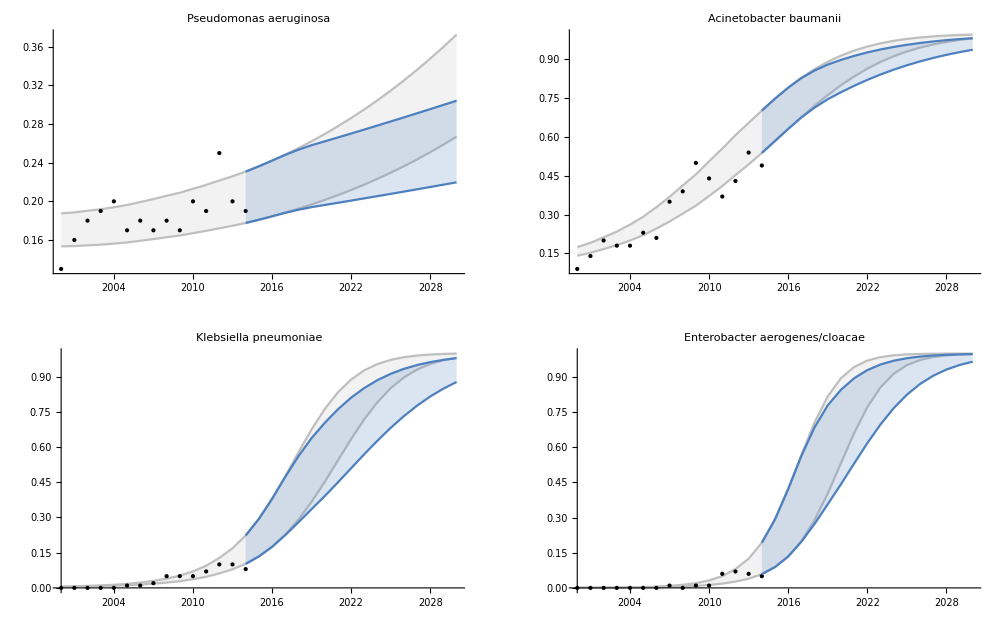
-Graphics-Stewardship (22% reduction in consumption by 2020)Resistance frequencyYears

```mathematica
title={"Formulary restrictions (95% reduction in consumption by 2018)","Formulary restrictions (95% reduction in consumption by 2020)","Stewardship (22% reduction in consumption by 2020)","Vaccine (~10% reduction in consumption by 2022)","Hand washing (7% reduction in consumption by 2020)"};
(*Export["Intervention_05.png",plots];*)

i=3;(*choose intervention to plot (out of 5)*)
Panel[GraphicsGrid[{{Show[plotM[[1]],plotD[[1]],plotS[[1]],plotP[[i]][[1]],PlotRange->All],Show[plotM[[2]],plotD[[2]],plotS[[2]],plotP[[i]][[2]],PlotRange->All,Axes->True,AxesOrigin->{2000,0.05}]},{Show[plotM[[3]],plotD[[3]],plotS[[3]],plotP[[i]][[3]],PlotRange->All],Show[plotM[[4]],plotD[[4]],plotS[[4]],plotP[[i]][[4]],PlotRange->All]}},ImageSize->1000],{Style[title[[i]],"Panel",24,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Years","Panel",18,Background->White]},{{Top,Center},{Left,Center},{Bottom,Center}},Appearance->"Frameless",Background->White]
```

# Economic & Health Outcomes

Note: current framework with dummy values (2017-2030)
*see cbp_params data sheet for parameters

### Mortality

```mathematica
np=data[[-1]][[-1]]*conbreak*0.11055; (*# pneumonia patients prescribed CBPs by pathogen*)

(*carbapenem prescription breakdown (empirical)*)
p={0.2,0.8,0.2,0.8}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*associated mortality rates {PA,AB,KP,EA/C}*)
m={{0.4,0.2,0.25,0.15,0.2,0.1,0.25,0.15},{0.4,0.2,0.25,0.15,0.2,0.1,0.25,0.15},{0.4,0.2,0.25,0.15,0.2,0.1,0.25,0.15},{0.4,0.2,0.25,0.15,0.2,0.1,0.25,0.15}}; (*resistant/susceptible: carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)
```

Status quo calculations {PA, AB, KP, EA/C}

```mathematica
(*yearly mortality calculations*)
ymSQm=Table[np[[i]]*(rSQms[[i]]*(p[[1]]*m[[i]][[1]] + p[[2]]*m[[i]][[2]]) + (1-rSQms[[i]])*(p[[1]]*m[[i]][[5]] + p[[2]] *m[[i]][[6]])),{i,1,nop}];(*lower bound*)
ymSQM=Table[np[[i]]*(rSQMs[[i]]*(p[[1]]*m[[i]][[1]] + p[[2]]*m[[i]][[2]]) + (1-rSQMs[[i]])*(p[[1]]*m[[i]][[5]] + p[[2]] *m[[i]][[6]])) ,{i,1,nop}];(*upper bound*)

(*total mortality, summed across 2017-2030*)
mSQm=Total[ymSQm,{2}];(*lower bound for different pathogens*)
mSQM=Total[ymSQM,{2}];(*upper bound for different pathogens*)
```

Intervention calculations {PA, AB, KP, EA/C}

```mathematica
ymIm=Table[intv[[j]]*ymSQm[[i]]+ (1-intv[[j]])*np[[i]]*((rIms[[j]][[i]]*(p[[3]]*m[[i]][[3]] + p[[4]]*m[[i]][[4]]) + (1-rIms[[j]][[i]])*(p[[3]]*m[[i]][[7]] + p[[4]] *m[[i]][[8]]))),{j,1,Length[intv]},{i,1,nop}]; (*min for different interventions for different pathogens*)
ymIM=Table[intv[[j]]*ymSQM[[i]]+  (1-intv[[j]])*np[[i]]*((rIMs[[j]][[i]]*(p[[3]]*m[[i]][[3]] + p[[4]]*m[[i]][[4]]) + (1-rIMs[[j]][[i]])*(p[[3]]*m[[i]][[7]] + p[[4]] *m[[i]][[8]]))),{j,1,Length[intv]},{i,1,nop}]; (*max for different interventions for different pathogens*)

mIm=Table[Total[ymIm[[i]],{2}],{i,1,Length[intv]}]; (*min for different interventions for different pathogens*)
mIM=Table[Total[ymIM[[i]],{2}],{i,1,Length[intv]}]; (*max for different interventions for different pathogens*)
```

#### Mortality plots

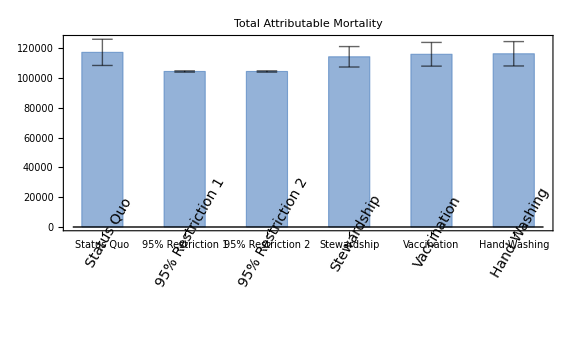

```mathematica
(*Total across all pathogens*)
mtotal=Join[{Mean[{Total[mSQm],Total[mSQM]}]},Mean[{Total[mIm,{2}],Total[mIM,{2}]}]]; (*plot mean of min and max*)
mcI=Join[{Total[mSQM]-Total[mSQm]},Total[mIM,{2}]-Total[mIm,{2}]];
labels={"Status Quo","95% Restriction 1","95% Restriction 2","Stewardship","Vaccination","Hand Washing"};

(*plot error bars and bar chart*)
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]

chartData=Table[mtotal[[i]]-> mcI[[i]],{i,1,Length[mtotal]}];

BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],
ChartLabels->Placed[labels,Axis,Rotate[Style[#,14,FontFamily-> "Calibri"],Pi/3]&],
Frame->Left,
FrameLabel->Automatic,
PlotLabel->"Total Attributable Mortality",
LabelStyle->Directive[Black,18, FontFamily-> "Calibri"],
BarSpacing-> 1,
FrameTicksStyle-> Directive[Black,14,FontFamily-> "Calibri"], 
ChartStyle->RGBColor[0.3,0.5,0.75,0.6],
ImageSize->Large]
```

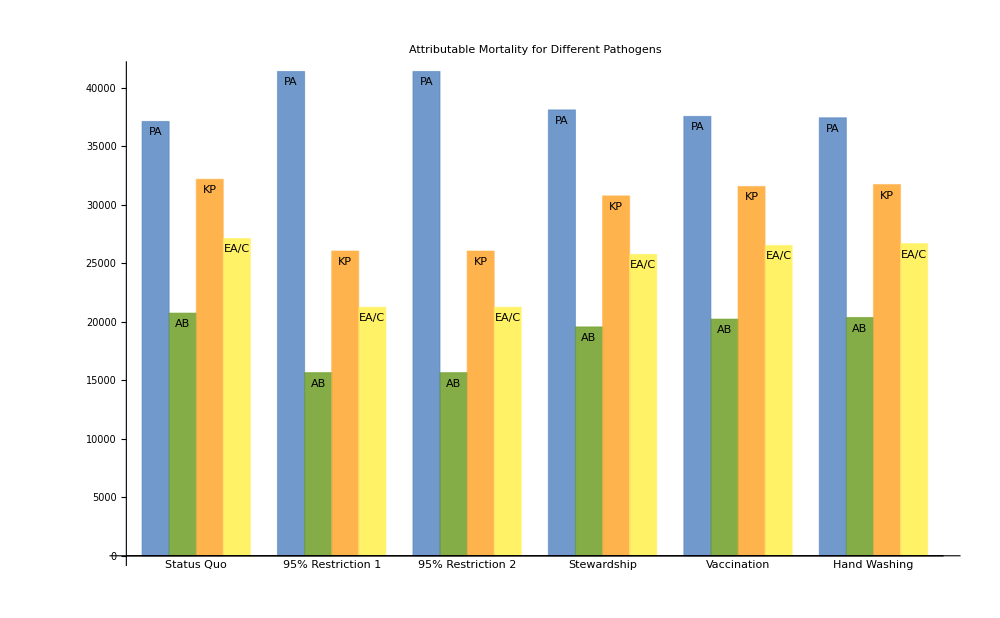

```mathematica
(*each pathogen plotted separately*)
pathlabels={"PA","AB","KP","EA/C"};
BarChart[Join[{Mean[{mSQm,mSQM}]},Mean[{mIm,mIM}]], 
ChartLabels->{Placed[labels,Below],Placed[pathlabels,Top]},
BaseStyle->Directive[FontFamily-> "Calibri", FontSize-> 14],
PlotLabel-> "Attributable Mortality for Different Pathogens",
AxesStyle-> Directive[Black, 14],
LabelStyle->Directive[Black,18],
BarSpacing-> {0,1},
ChartStyle-> {RGBColor[0.3,0.5,0.75,0.8],  RGBColor[0.4,0.6,0.1,0.8], RGBColor[1,0.7,0.3],RGBColor[1,0.95,0.4]},
ImageSize-> 1000]
```

### Length of Stay

```mathematica
(*attributable length of stay {PA,AB,KP,EA/C}*)
los={{5,3,4,2,3,2,4,3},{5,3,4,2,3,2,4,3},{5,3,4,2,3,2,4,3},{5,3,4,2,3,2,4,3}};  (*resistant/susceptible: carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*) 

(*general ward cost/day*)
gw=2877;
```

Status quo calculations {PA, AB, KP, EA/C}

```mathematica
(*yearly LOS calculations*)
ylSQm=Table[np[[i]]*(rSQms[[i]]*(p[[1]]*los[[i]][[1]] + p[[2]]*los[[i]][[2]]) + (1-rSQms[[i]])*(p[[1]]*los[[i]][[5]] + p[[2]] *los[[i]][[6]])) ,{i,1,nop}];(*lower bound*)
ylSQM=Table[np[[i]]*(rSQMs[[i]]*(p[[1]]*los[[i]][[1]] + p[[2]]*los[[i]][[2]]) + (1-rSQMs[[i]])*(p[[1]]*los[[i]][[5]] + p[[2]] *los[[i]][[6]])) ,{i,1,nop}];(*upper bound*)

(*total LOS, summed across 2017-2030*)
lSQm=Total[ylSQm,{2}];(*lower bound for each pathogen*)
lSQM=Total[ylSQM,{2}];(*upper bound for each pathogen*)
```

Intervention calculations {PA, AB, KP, EA/C}

```mathematica
(*yearly LOS calculations*)
ylIm=Table[intv[[j]]*ylSQm[[i]]+  (1-intv[[j]])*np[[i]]*((rIms[[j]][[i]]*(p[[3]]*los[[i]][[3]] + p[[4]]*los[[i]][[4]]) + (1-rIms[[j]][[i]])*(p[[3]]*los[[i]][[7]] + p[[4]] *los[[i]][[8]]))),{j,1,Length[intv]},{i,1,nop}]; (*lower bound*)
ylIM=Table[intv[[j]]*ylSQM[[i]]+  (1-intv[[j]])*np[[i]]*((rIMs[[j]][[i]]*(p[[3]]*los[[i]][[3]] + p[[4]]*los[[i]][[4]]) + (1-rIMs[[j]][[i]])*(p[[3]]*los[[i]][[7]] + p[[4]] *los[[i]][[8]]))),{j,1,Length[intv]},{i,1,nop}]; (*upper bound*)

(*total LOS, summed across 2017-2030*)
lIm=Table[Total[ylIm[[i]],{2}],{i,1,Length[intv]}]; (*lower bound for each intervention & each pathogen*)
lIM=Table[Total[ylIM[[i]],{2}],{i,1,Length[intv]}]; (*upper bound for each intervention & each pathogen*)
```

#### Length of stay plots

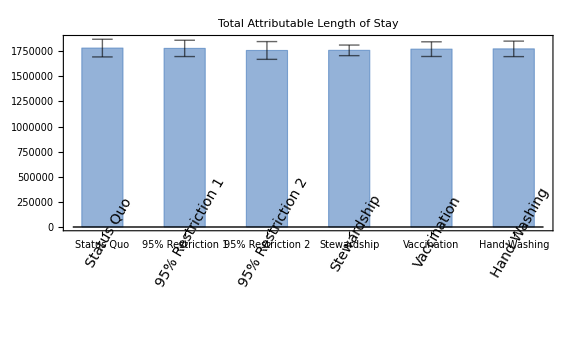

```mathematica
(*Total across all pathogens*)
ltotal=Join[{Mean[{Total[lSQm],Total[lSQM]}]},Mean[{Total[lIm,{2}],Total[lIM,{2}]}]]; (*plot mean of lower and upper bounds*)
lcI=Join[{Total[lSQM]-Total[lSQm]},Total[lIM,{2}]-Total[lIm,{2}]];
labels={"Status Quo","95% Restriction 1","95% Restriction 2","Stewardship","Vaccination","Hand Washing"};

(*plot error bars and bar chart*)
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]

chartData=Table[ltotal[[i]]-> lcI[[i]],{i,1,Length[mtotal]}];

BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],
ChartLabels->Placed[labels,Axis,Rotate[Style[#,14,FontFamily-> "Calibri"],Pi/3]&],
Frame->Left,
FrameLabel->Automatic,
PlotLabel->"Total Attributable Length of Stay",
LabelStyle->Directive[Black,18, FontFamily-> "Calibri"],
BarSpacing-> 1,
FrameTicksStyle-> Directive[Black,14,FontFamily-> "Calibri"], 
ChartStyle->RGBColor[0.3,0.5,0.75,0.6],
ImageSize->Large]
```

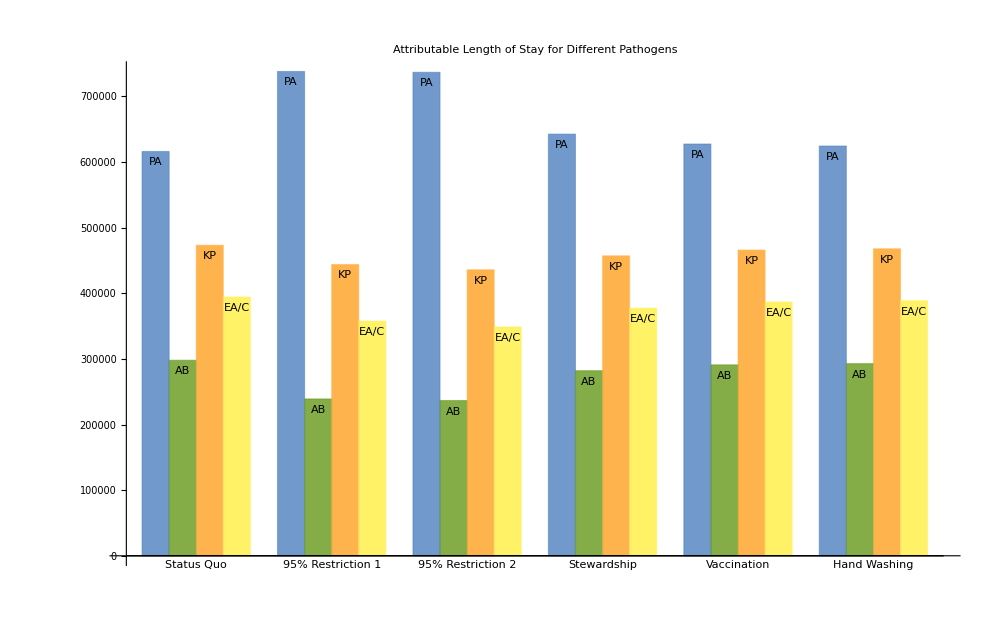

```mathematica
(*each pathogen plotted separately*)
BarChart[Join[{Mean[{lSQm,lSQM}]},Mean[{lIm,lIM}]], 
ChartLabels->{Placed[labels,Below],Placed[pathlabels,Top]},
BaseStyle->Directive[FontFamily-> "Calibri", FontSize-> 14],
PlotLabel-> "Attributable Length of Stay for Different Pathogens",
AxesStyle-> Directive[Black, 14],
LabelStyle->Directive[Black,18],
BarSpacing-> {0,1},
ChartStyle-> {RGBColor[0.3,0.5,0.75,0.8],  RGBColor[0.4,0.6,0.1,0.8], RGBColor[1,0.7,0.3],RGBColor[1,0.95,0.4]},
ImageSize-> 1000]
```

### Net Health Benefit

#### Costs

Ward costs: assuming general ward costs for all length of stay days (2017-2030)

```mathematica
wSQm=ylSQm*gw; (*SQ, lower bound*)
wSQM=ylSQM*gw;(*SQ, upper bound*)

wIm=ylIm*gw; (*I, lower bound*)
wIM=ylIM*gw;(*I, upper bound*)
```

Antimicrobial costs: calculated using pneumonia prevalence and treatment duration (2017-2030)
*assuming future prevalence for all years is equivalent to prevalence during the last year data is available

```mathematica
c={107.5,600,110,600};(*cost per daily dose ($): carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)
tlength=7.5; (*treatment length for pneumonia patients*)

(*status quo*)
cbpcostSQ=(data[[-1]][[-1]]*tlength)*(Table[p[[1]]*cbpSQ[[i]][[-14;;All]],{i,1,nop}]*c[[1]] )+(Table[p[[2]]*cbpSQ[[i]][[-14;;All]],{i,1,nop}]*c[[2]] );

(*interventions*) 
cbpcostI=Table[intv[[i]]*cbpcostSQ,{i,1,Length[intv]}]+
(1-intv)*(data[[-1]][[-1]]*tlength)*((Table[p[[3]]*cbpI[[i]][[j]][[-14;;All]],{i,1,Length[intv]},{j,1,nop}]*c[[3]])+(Table[p[[4]]*cbpI[[i]][[j]][[-14;;All]],{i,1,Length[intv]},{j,1,nop}]*c[[4]]));
```

Total associated costs: ward costs + antimicrobial costs (currently not including indirect costs of caregivers)

```mathematica
cSQm=wSQm + cbpcostSQ; (*SQ cost lower bound*)
cSQM=wSQM+cbpcostSQ; (*SQ cost upper bound*)

cIm=wIm+cbpcostI; (*I cost lower bound*)
cIM=wIM + cbpcostI;(*I cost upper bound*)
```

#### QALYs

```mathematica
uP=0.969; (*utility weight for pneumonia patients while sick*)
ageP=65; (*average age at death (pneumonia)*)
le=78.8; (*average life expectancy in the US*)

(*STATUS QUO*)
qSQm=(data[[-1]][[-1]]*conbreak*le )-(ylSQm*(1-uP))-(ymSQm*(le-ageP)); (*lower bound*)
qSQM=(data[[-1]][[-1]]*conbreak*le )-(ylSQM*(1-uP))-(ymSQM*(le-ageP)); (*upper bound*)

(*INTERVENTIONS*)
qIm=Table[(data[[-1]][[-1]]*conbreak*le )-((ylIm*(1-uP))-(ymIm*(le-ageP)))[[i]],{i,1,Length[intv]}]; (*lower bound for each pathogen*)
qIM=Table[(data[[-1]][[-1]]*conbreak*le )-((ylIm*(1-uP))-(ymIm*(le-ageP)))[[i]],{i,1,Length[intv]}]; (*upper bound for each pathogen*)
```

#### Net Health Benefit Plots

```mathematica
wtp=50000 ;(*willingness to pay threshold*)
nhbSQ=Join[{qSQm-(cSQm/wtp)},{qSQM-(cSQM/wtp)}]; (*net health benefit under status quo {lower bound, upper bound}*)
nhbI=Join[{qIm-(cIm/wtp)},{qIm-(cIm/wtp)}];(*net health benefit under interventions {lower bound, upper bound}*)
```